# Data Science and Machine Learning

## Lab session 11: Neural Nets

Neural networks are a programming approach that is inspired by the neurons in the human brain and enables computers to learn from observational data: be it images, audio, text, or numbers. They try to model some unknown function (for example,  f: P→Q) that maps this data into numbers or classes by recognizing patterns in the data. 

Here is a very well done introduction to Neural Networks:

```mathematica
EmbeddedHTML["<iframe width='854' height='510' src='//www.youtube.com/embed/aircAruvnKk' frameborder='0' allowfullscreen></iframe>"]
```

Null<iframe width='854' height='510' src…eborder='0' allowfullscreen></iframe><iframe width='854' height='510' src='//www.youtube.com/embed/aircAruvnKk' frameborder='0' allowfullscreen></iframe>

For more info: https://www.3blue1brown.com/topics/neural-networks

Free online book on neural networks: Neural Networks and Deep Learning, by Michael Nielsen

## How to build and train your own Neural Net?

Neural Nets are built from the following components:

Encoders and decoders (to convert the input data type to numeric tensors)

Layers (to perform operations on these tensors depending on the applications)

Containers (to hold these operations in a sensible way)

### Network data: tensors, encoders & decoders

#### Tensors

Tensors are multidimensional arrays:
	- Rank 0 (scalars): 0.0
    	- Rank 1 (vectors): {0.0, 1.0}  
        	- Rank 2 (matrices): {{1., 2., 3.} , {3., 2., 1.}}
            	- Rank n tensors: {... {... {1., 2., 3.}...}...}

Examples of tensors:

Coordinates of points as vectors:

```mathematica
data={{2,4},{3,3},{1,2}};
plot=ListPlot[Labeled[#,Framed[#,FrameStyle->None]]&/@data,Frame->True,LabelStyle->Medium,AspectRatio->1,PlotRangePadding->1,PlotStyle->PointSize[0.04],ImageSize->Small];
gr=Grid[{{Style["(",20],Style[2,20],Spacer[1],Style[4,20],Style[")",20]},{Style["(",20],Style[3,20],Spacer[1],Style[3,20],Style[")",20]},{Style["(",20],Style[1,20],Spacer[1],Style[2,20],Style[")",20]}}];Row[{plot, Spacer[60], Style["  ≈ ",32], Spacer[60], gr}]
```

-Graphics-  ≈ ( | 2 |  | 4 | )
( | 3 |  | 3 | )
( | 1 |  | 2 | )

Matrices as grayscale images:

```mathematica
Row[{ArrayPlot[DiskMatrix[5],Mesh->All,ImageSize->200], Spacer[60], Style["  ≈ ",32], Spacer[60], MatrixForm@DiskMatrix[4]}]
```

-Graphics-  ≈ (0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

Rank-3 tensors as colored images:

```mathematica
re={1,1,0};bl={1,0,1};gr={0,1,1};data={{re,bl,bl},{re,gr,bl},{re,re,bl}};img=Image[data];Row[{ArrayPlot[ImageData@img,ColorFunction->RGBColor,Mesh->True,ImageSize->200], Spacer[60], Style["  ≈ ",32], Spacer[60],MatrixForm[{MatrixForm/@Round[Transpose[data,{2,3,1}]]}]}]
```

-Graphics-  ≈ ((1 | 1 | 1
1 | 0 | 1
1 | 1 | 1) | (1 | 0 | 0
1 | 1 | 0
1 | 1 | 0) | (0 | 1 | 1
0 | 1 | 1
0 | 0 | 1))

#### Net Encoders & Decoders

NetEncoder convert non-numerical data (e.g., images, texts, audios, videos) to net-compatible numerical arrays.
There are many format and available encoders/decoders.

```mathematica
dog=-Graphics-;
```

```mathematica
encImage = NetEncoder[{"Image",ColorSpace->"RGB", ImageDimensions[dog]}]
dogEncoded =encImage[dog];
Dimensions[dogEncoded]
```

NetEncoder[…]

{3,162,243}

To convert back a numerical array to the original format, you can use NetDecoder:

```mathematica
decImage=NetDecoder[{"Image",ColorSpace->"RGB"}];
decImage[dogEncoded]
```

-Graphics-

Here is another illustration, with text.
It converts the words in a string to a sequence of integer codes using a standard English vocabulary, or another language that you can specify as option.

```mathematica
encText = NetEncoder["Tokens"];
textEncoded =encText["hello world"]
```

{15753,38973}

### Layers

A neural network is a biologically inspired model and consists of “layers” or “neurons” through which information is processed from the input to the output tensor. Layers are usually defined by their mathematical operation.

#### Implemented layers

The implemented layers in the Wolfram Language are:

```mathematica
{{"Layer Type", "Layers"}, {"Basic Layers ", "LinearLayer | ElementwiseLayer | SoftmaxLayer"}, {"Custom Layers ", "FunctionLayer | CompiledLayer | PlaceholderLayer | ElementwiseLayer | ThreadingLayer | RandomArrayLayer"}, {"Array Operation Layers", "NetArrayLayer | SummationLayer  | TotalLayer | AggregationLayer  | DotLayer | OrderingLayer"}, {"Convolution and Filtering Layers", "ConvolutionLayer | DeconvolutionLayer | PoolingLayer | ResizeLayer |  SpecialTransformationLayer"}, {"Training Optimization Layers", "ImageAugmentationLayer | BatchNormalizationLayer | DropoutLayer | LocalResponseNormalizationLayer | NormalizationLayer"}, {"Structure Manipulation Layers", "CatenateLayer | PrependLayer | AppendLayer  | FlattenLayer | ReshapeLayer | ReplicateLayer |  PaddingLayer | PartLayer | TransposeLayer| ExtractLayer"}, {"Array Operation Layers", "NetArrayLayer | SummationLayer | TotalLayer | AggregationLayer | DotLayer | OrderingLayer"}, {"Recurrent Layers", "BasicRecurrentLayer |  GatedRecurrentLayer | LongShortTermMemoryLayer"}, {"Sequence-Handling Layers", "EmbeddingLayer | SequenceLastLayer | SequenceReverseLayer | SequenceMostLayer | SequenceRestLayer | AttentionLayer | UnitVectorLayer| AppendLayer| PrependLayer"}}
```

#### Linear Layer

A LinearLayer is an affine transformation x→Ax+b, where A is the “weight matrix” and the vector b is the “bias vector”.

Every neuron of the top array is connected with the bottom array, resulting in n×n connections.

Hence, n×n weights and n biases have to be learned.

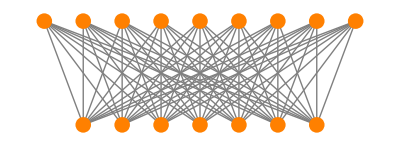

```mathematica
Block[
{h=4,r=0.3,layer0Pts,layer1Pts},
layer0Pts=Thread[{1.5 Range[0,8],h}];
layer1Pts=Thread[{1.5 Range[1,7],0}];
Graphics[
{{Gray,Outer[Line[{##}]&,layer0Pts,layer1Pts,1]},
{FaceForm[Orange],Map[Disk[#,r]&,layer0Pts],Map[Disk[#,r]&,layer1Pts]}
}
]
]
```

#### Elementwise Layer

The ElementwiseLayer applies a unary function f to every element of the input tensor:

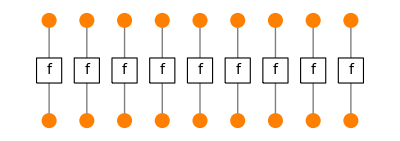

```mathematica
Block[
{h=4,r=0.3,layer0Pts,layer1Pts},
layer0Pts=Thread[{1.5 Range[0,8],h}];
layer1Pts=Thread[{1.5 Range[0,8],0}];
Graphics[
{{Gray,MapThread[Line[{##}]&,{layer1Pts,layer0Pts}]},
{FaceForm[White],EdgeForm[{Thin,Black}],Map[{Rectangle[#-1/2,#+1/2],Text[Style["f",14],#]}&,Thread[{1.5 Range[0,8],h/2}]]},
{FaceForm[Orange],Map[Disk[#,r]&,layer0Pts],Map[Disk[#,r]&,layer1Pts]}
}
]
]
```

The function f is referred to as the activation function in literature; common choices for this so-called activation function are LogisticSigmoid, Tanh, Ramp (rectified linear unit, ReLU):

```mathematica
Row[Table[
{min,max}={-1,1}*If[f===Ramp,1,3];
Plot[f[x],{x,min,max},PlotLabel->f,ImageSize->200,Frame->True,PlotRange->{{min,max},{-1,1}},AspectRatio->0.5,FrameTicks->{{{-1,0,1},{}},{{min,0,max},{}}}],{f,{LogisticSigmoid,Tanh, Ramp}}], Spacer[50]]
```

-Graphics--Graphics--Graphics-

#### SoftMax Layer

The SoftMaxLayer takes a vector as input and returns normalized exponential values as class probabilities. The element x in a vector is converted to e/∑e,  and generally the innermost dimension is used as the normalization dimension.

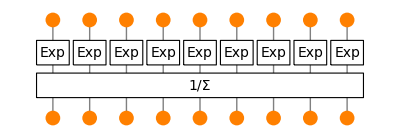

```mathematica
Block[
{h=4,r=0.3,layer0Pts,layer1Pts},
layer0Pts=Thread[{1.5 Range[0,8],h}];
layer1Pts=Thread[{1.5 Range[0,8],0}];
Graphics[
{{Gray,MapThread[Line[{##}]&,{layer1Pts,layer0Pts}]},
{FaceForm[White],EdgeForm[{Thin,Black}],Map[{Rectangle[#-{2/3,1/2},#+{2/3,1/2}],Text[Style["Exp",14],#]}&,Thread[{1.5 Range[0,8],2h/3}]],
Rectangle[{0,h/3}-{2/3,1/2},{12,h/3}+{2/3,1/2}],Text[Style["1/Σ",14],{6,h/3}]},
{FaceForm[Orange],Map[Disk[#,r]&,layer0Pts],Map[Disk[#,r]&,layer1Pts]}
}
]
]
```

#### Convolution Layer

A ConvolutionLayer will apply convolution on a tensor, usually performing a downsampling/ filtering operation. It takes a kernel (square or rectangular), stride and padding to create the output. This is the core building block of convolution neural networks (CNNs). CNNs often have several levels of convolution layers, which pick up patterns at different levels of detail (recognize large structures, then smaller patterns, etc.). Conceptually, you replace a section of pixels in an image with a weighted average of their values. The weights are the parameters of the layer.

#### Pooling Layer

A form of nonlinear downsampling, often used in CNNs in between convolution layers. The functions that could be used are Max, Mean, Total.

### Building your Neural Net (containers)

#### Stacking Layers in a chain: NetChain

A neural network is essentially a function f with adjustable weights w mapping an input question x into an output answer y :

```mathematica
Subscript[f, w](x)↦y
```

Neuronal networks are structured in layers constituting a nesting of functions:

```mathematica
h(g(f(x)))↦y
```

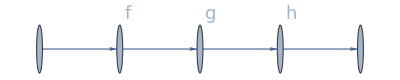

```mathematica
Graph[{1->2,2->3,3->4,4->5},VertexLabels->{2-> Style["f",18],3-> Style["g",18],4-> Style["h",18]}]
```

NetChain can be used to connect different layers in a chain-like fashion to create a neural net

Let's start with a single layer.
We simply applying the hyperbolic tangent function (Tanh) to the data:

```mathematica
net=NetChain[{ElementwiseLayer[Tanh]}]
net[{-1,0,1}]
Tanh[{-1,0,1}]//N
```

NetChain[…]

{-0.761594,0.,0.761594}

{-0.761594,0.,0.761594}

Let's now can combine several several functions.

```mathematica
NetChain[{LinearLayer[3],ElementwiseLayer[Tanh],LinearLayer[4],ElementwiseLayer[Ramp],LinearLayer[5]}]
```

NetChain[…]

Here is what is happening:
	1. convert our input array into a vector of size 3, 
    	2. apply the hyperbolic tangent function,
        	3. convert the result into a vector of size 4,
            	4. apply the Ramp function - Ramp[x] returns x if positive, 0 otherwise,
               5. convert the result into a vector of size 5

The syntax above can be shortened:
	LinearLayer[n] 		is equivalent to simply specifying n
    	ElementwiseLayer[f] 	is equivalent to simply specifying f

```mathematica
NetChain[{3,Tanh,4,Ramp,5}]
```

NetChain[…]

#### Building more complex Neural Nets: NetGraph

Non-cyclic graphs can also be used to represent the function f:

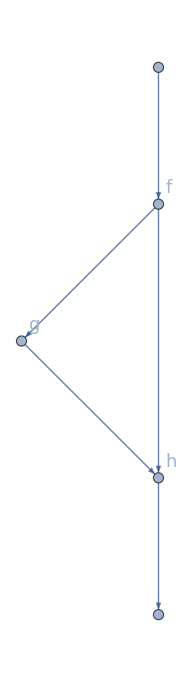

```mathematica
Graph[{1->2,2->3,2->4,3->4,4->5},VertexLabels->{2-> Style["f",18],3-> Style["g",18],4-> Style["h",18]},ImageSize->Small]
```

This is done in the Wolfram Language using NetGraph. 
NetGraph can be used to connect different layers to create a graphical neural network of any topology.

```mathematica
NetGraph[{2,Ramp,4,Ramp,8},{1->2->3->4->5}]
NetChain[{2,Ramp,4,Ramp,8}]
```

NetGraph[…]

NetChain[…]

We can build more complex Neural Nets:

```mathematica
net=NetGraph[{Ramp,Tanh,Times,Plus},{1->2->3,1->3->4,2->4}]
```

NetGraph[…]

The seemingly complicated network structure is actually doing the following operation:

```mathematica
data={-2,-1,0,1,2}
net[data]
Tanh@Ramp@data*Ramp@data+Tanh@Ramp@data//N
```

{-2,-1,0,1,2}

{0.,0.,0.,1.52319,2.89208}

{0.,0.,0.,1.52319,2.89208}

#### Dealing with several inputs/outputs: NetPort

Sometimes you want to create graphs that perform operations on several inputs, or features:

```mathematica
h(g(x),f(x))↦y
```

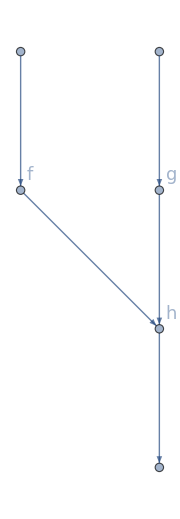

```mathematica
Graph[{1->2,3->4,2->5,4->5,5->6},VertexLabels->{2-> Style["f",18],4-> Style["g",18],5-> Style["h",18]},ImageSize->Small]
```

NetPort represents the specified port for a layer in a NetGraph or similar structure.

For instance, let's create a simple NetGraph with two inputs

```mathematica
NetGraph[{Ramp,LogisticSigmoid,TotalLayer[]},{NetPort["Input1"]->1,NetPort["Input2"]->2,{1,2}->3}]
```

NetGraph[…]

Similarly, when you want to generate several outputs:

```mathematica
NetGraph[{Ramp,LogisticSigmoid},{1->2,1->NetPort["Output1"],2->NetPort["Output2"]}]
```

NetGraph[…]

### Training your Neural Net

When we built our neural net, we specified a function f with parameters (weights) w. 
Training consists in finding these parameters, using data. Neural networks are thus data-driven algorithms.

#### How neural networks learn?

From a set of inputs observations, our goal is to generate outputs that are "close" to the actual "true" value. 
In other words, we want to minimize the errors between the predicted value and the true outcome.

```mathematica
EmbeddedHTML["<iframe width='854' height='510' src='//www.youtube.com/embed/IHZwWFHWa-w' frameborder='0' allowfullscreen></iframe>"]
```

Null<iframe width='854' height='510' src…eborder='0' allowfullscreen></iframe><iframe width='854' height='510' src='//www.youtube.com/embed/IHZwWFHWa-w' frameborder='0' allowfullscreen></iframe>

We first need to measure our prediction error by defining a loss function L between our prediction and our actual outcome:

```mathematica
L[Subscript[f, w][x],y]
```

Some loss functions that we have seen before: Least Square Errors (used in regression), Logistic loss (used in classification).

Training a network finds a (local) optimum of the loss as a function of the learned parameters.

To find the solution of our problem, we use numerical optimization: we search the minimum by iteration.

To update the parameters, we are using the gradient descent method.

The gradient ∂L determines the change of weights w in order to decrease L:

```mathematica
D[L(Subscript[f, w](x),y), w]= (∂L(Subscript[f, w](x),y))/(∂f) (∂Subscript[f, w](x))/(∂w)
```

To train parameters, the error or cost function or loss ϵ of the network is computed on the entire training data. The chain rule is used to back-propagate the error ϵ through the network (full batch gradient descent).

However, when the data is repetitive or too large, the error or loss or cost function ϵ of the network is computed on  subsets (or batches) of training data (mini-batch gradient descent/stochastic gradient descent).

```mathematica
w ↦w+Δw           Δw==-η ∑_(k∈B) ∂_w L(Subscript[f, w](Subscript[x, k]),Subscript[y, k])
```

The parameters of the network gradually converge on a local optimum, i.e. the error is minimized.

In practice, more complicated update schemes can be used...

#### Training in practice: TrainNet

For training a neural network, the function NetTrain is used. 
NetTrain performs a lot of operations automatically: it will initialize the parameters in the layers and decide on the initial learning rate, the method for updating the parameters, the learning rate schedule, the batch size and the loss functions to use. However, you can modify the default options.

Let's say we have a simple classifier, consisting of one LinearLayer and one LogisticSigmoid layer:

```mathematica
net = NetChain[{LinearLayer[], LogisticSigmoid}]
```

NetChain[…]

We train our model by providing a training set:

```mathematica
training = {0.7 ->False, 1 -> False,1.2->False, 2 -> False,1.5-> False, 2.3->False,2.8 -> True,3 -> True,3.1->True, 4 -> True, 4.9 ->True};
```

```mathematica
netTrained =  NetTrain[net, training]
```

NetChain[…]

We can now test our model:

```mathematica
netTrained[3.7]
```

True

To get the probability of belonging to a class, we can disable the NetDecoder, i.e. the layer that transforms the result of the LogisticSigmoid operation (probability) into our class (True or False)

```mathematica
Plot[netTrained[x, None], {x, 0, 5}]
```

-Graphics-

You can generate a NetTrainResultsObject to obtain detailed information about the training process

```mathematica
result = NetTrain[net, training, All]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:11s  examples/s:10179
data | ,,  training examples:11  processed examples:110000  skipped examples:0
method | ,,  ADAMoptimizer  batch size11CPU
round | ,,  loss:1.09×10^-1  error:0%
 | 
 | ]

### Evaluate the performance of your Neural Net

Similar to what we did when using Predict/PredictorMeasurements and Classify/ClassifierMeasurements, NetMeasurements allow to compute measurements about our model.

```mathematica
test = {1.7 ->False, 2.6 -> False,3.4 -> True, 4.3 -> True};
NetMeasurements[netTrained,test,"Accuracy"]
NetMeasurements[netTrained, test, "ConfusionMatrixPlot"]
```

0.75

actual class | -Graphics-
 | predicted class

Note that you could also use ClassifierMeasurements:

```mathematica
ClassifierMeasurements[netTrained,test]
```

Classifier Measurements
Classifier method | Net
Number of test examples | 4
Accuracy | (75.25.) %
Accuracy baseline | (50.29.) %
Geometric mean of probabilities | 0.678 ± 0.12
Mean cross entropy | 0.389 ± 0.18
Single evaluation time | 1.65 ms/example
Batch evaluation speed | 278. examples/s
-Graphics- |

## Some applications

### Gaussian

We will perform a simple linear classification task consisting in identifying two mostly separated Gaussians:

Create an artificial dataset from two normally distributed clusters and plot this dataset

```mathematica
makeCluster[class_,μ_,σ_]:=RandomVariate[BinormalDistribution[{μ,μ},{σ,σ},0],1000]->class;
clusters=makeCluster@@@{{Red,1,0.5},{Green,-1,0.5}};
plot=ListPlot[Keys[clusters], PlotStyle->{RGBColor[0.8, 0., 0.],RGBColor[0., 0.8, 0.]},AspectRatio->1,Frame->True,PlotRange->{{-3,3},{-3,3}}]
```

-Graphics-

The training data consists of rules mapping the point to the cluster it is in:

```mathematica
trainingData=Flatten[Thread/@clusters];
RandomSample[trainingData,6]
```

{{-1.34417,-0.447814}→RGBColor[0, 1, 0],{1.76708,1.20051}→RGBColor[1, 0, 0],{0.0336249,-0.248992}→RGBColor[0, 1, 0],{0.636385,0.714113}→RGBColor[1, 0, 0],{0.793781,1.99559}→RGBColor[1, 0, 0],{1.28291,1.51263}→RGBColor[1, 0, 0]}

Create a net to compute the probability of a point lying in each cluster, using a "Class" decoder to classify the input as either Red or Green:

```mathematica
net=NetChain[{4 , (*First fully-connected layer*)
                          2,      (*Corresponds to 2 classes *)
                          SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,Green}}]]
```

NetChain[…]

Train the net on the data:

```mathematica
trained=NetTrain[net,trainingData]
```

NetChain[…]

Show the contours in feature space in which each class reaches a posterior probability of 0.75:

```mathematica
Show[plot,Quiet@Table[ContourPlot[trained[{x,y},{"Probability",color}]==0.75,{x,-5,5},{y,-5,5},ContourStyle->{Thick,Darker[color,.3]}],{color,{Red,Green}}]]
```

-Graphics-

### XOR

The XOR classification problem is one of the simplest examples where linear classification fails.

Create an artificial dataset for XOR classification:

```mathematica
makeCluster[class_,r1_,r2_,r3_,r4_]:=RandomVariate[UniformDistribution[{{r1,r2}, {r3, r4}}],500]->class;
clusters=makeCluster@@@{{Red,0,3,0,3},{Red,-3,0,-3,0},{Green,-3,0,0,3},{Green,0,3,-3,0}};
plot=ListPlot[Keys[clusters], PlotStyle->{RGBColor[0.8, 0., 0.],RGBColor[0.8, 0., 0.],RGBColor[0., 0.8, 0.],RGBColor[0., 0.8, 0.]},AspectRatio->1,Frame->True,PlotRange->{{-3,3},{-3,3}}]
```

-Graphics-

```mathematica
trainingData=Flatten[Thread/@clusters];
net=NetChain[{10 , (*First fully-connected layer*)
                          Ramp, (*To provide the non-linearity required to draw the surfaces *)
                          2,      (*Corresponds to 2 classes*)
                          SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,Green}}]]
```

NetChain[…]

Training and visualization:

```mathematica
trained=NetTrain[net,trainingData]
Show[plot,Quiet@Table[ContourPlot[trained[{x,y},{"Probability",color}]==0.75,{x,-5,5},{y,-5,5},ContourStyle->{Thick,Darker[color,.3]}],{color,{Red,Green}}]]
```

NetChain[…]

-Graphics-

### Classify handwritten digits

We build a Convolution Network called LeNet, one of the first convolutional nets.

```mathematica
lenet=NetChain[{
(*STEP 1: FEATURE EXTRACTION*)
       (*FIRST CONVOLUTION BLOCK*) 
ConvolutionLayer[20,5],(*first convolution => 20 feature images*)
Ramp,  (*activation function (ReLU) => non-linearity, sparsity*)
(*FIRST POOLING BLOCK*)
PoolingLayer[2,2],  (*max pooling => downsampling*)
(*SECOND CONVOLUTION BLOCK*)
ConvolutionLayer[50,5],(*second convolution => 50 feature images*)
Ramp,
(*SECOND POOLING BLOCK*)
PoolingLayer[2,2],
FlattenLayer[],(*flattening => images to vector*)
(*STEP 2: COMPUTING CLASS PROBABILITY*)
(*FULLY-CONNECTED BLOCK 1*)
500,(*first fully connected layer => feature vector from image features*)
Ramp,
(*FULLY-CONNECTED BLOCK 2*)
10,(*second fully connected layer => class prediction*)
(*PROBABILITY COMPUTATIONS*)
SoftmaxLayer[]},(*normalization*)
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}], (*encoder => image to tensor*)"Output"->NetDecoder[{"Class",Range[0,9]}]  (*decoder => tensor to class*)
]
```

NetChain[…]

We train LeNet on the handwritten digits from the MNIST database:

```mathematica
trainingData=ResourceData[ResourceObject["MNIST"],"TrainingData"];
testData=ResourceData[ResourceObject["MNIST"],"TestData"];
randomData = RandomSample[trainingData,3]
```

{-Graphics-→5,-Graphics-→2,-Graphics-→4}

Let's train our model. 
Try to improve the speed, we change the number of MaxTrainingRounds to 2 and we change the BatchSize, which improves the number of inputs per second:

```mathematica
trained=NetTrain[lenet,trainingData,All,MaxTrainingRounds->2,BatchSize->512 ]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:236  rounds:2  time:1.4min  examples/s:1408
data | ,,  training examples:60000  processed examples:120832  skipped examples:0
method | ,,  ADAMoptimizer  batch size512CPU
round | ,,  loss:7.89×10^-2  error:2.35%
 | 
 | ]

```mathematica
trainedNet = trained["TrainedNet"]
```

NetChain[…]

We can extract some properties of our model:

```mathematica
trained["FinalPlots"]
```

<|Loss→ | rounds
loss | -Graphics-,ErrorRate→ | rounds
error rate | -Graphics-|>

In the Wolfram Language, it is very easy to visualize the underlying features each layer is extracting. It is common to find out that the first few layers extract more of the coarse features, the obvious patterns, while the later layers extract the finer features.

Let's find out what the first convolution layer sees:

```mathematica
conv1=NetTake[trainedNet,2]
```

NetChain[…]

```mathematica
Image/@conv1[-Graphics-]
Image/@conv1[-Graphics-]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Similarly, let's find out what the second convolution layer sees:

```mathematica
conv2=NetTake[trainedNet,5]
Image/@conv2[-Graphics-]
Image/@conv2[-Graphics-]
```

NetChain[…]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Finally, let's see how our model performs on the testing set:

```mathematica
ClassifierMeasurements[trainedNet,testData]
```

Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (98.140.14) %
Accuracy baseline | (11.350.32) %
Geometric mean of probabilities | 0.941 ± 0.0031
Mean cross entropy | 0.0607 ± 0.0033
Single evaluation time | 2.54 ms/example
Batch evaluation speed | 3.07 examples/ms
-Graphics- |

## Wolfram Neural Net Repository

NetModel allows to obtain already trained neural networks model from the Wolfram Neural Net Repository

```mathematica
NetModel[]
```

{2D Face Alignment Net Trained on 300W Large Pose Data,3D Face Alignment Net Trained on 300W Large Pose Data,AdaIN-Style Trained on MS-COCO and Painter by Numbers Data,Ademxapp Model A1 Trained on ADE20K Data,Ademxapp Model A1 Trained on Cityscapes Data,Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data,Ademxapp Model A Trained on ImageNet Competition Data,Age Estimation VGG-16 Trained on IMDB-WIKI and Looking at People Data,Age Estimation VGG-16 Trained on IMDB-WIKI Data,BERT Trained on BookCorpus and Wikipedia Data,BioBERT Trained on PubMed and PMC Data,BPEmb Subword Embeddings Trained on Wikipedia Data,CapsNet Trained on MNIST Data,Clinical Concept Embeddings Trained on Health Insurance Claims, Clinical Narratives from Stanford and PubMed Journal Articles,Colorful Image Colorization Trained on ImageNet Competition Data,ColorNet Image Colorization Trained on ImageNet Competition Data,ColorNet Image Colorization Trained on Places Data,ConceptNet Numberbatch Word Vectors V17.06,ConceptNet Numberbatch Word Vectors V17.06 (Raw Model),CREPE Pitch Detection Net Trained on Monophonic Signal Data,CycleGAN Apple-to-Orange Translation Trained on ImageNet Competition Data,CycleGAN Horse-to-Zebra Translation Trained on ImageNet Competition Data,CycleGAN Monet-to-Photo Translation,CycleGAN Orange-to-Apple Translation Trained on ImageNet Competition Data,CycleGAN Photo-to-Cezanne Translation,CycleGAN Photo-to-Monet Translation,CycleGAN Photo-to-Van Gogh Translation,CycleGAN Summer-to-Winter Translation,CycleGAN Winter-to-Summer Translation,CycleGAN Zebra-to-Horse Translation Trained on ImageNet Competition Data,Deep Speech 2 Trained on Baidu English Data,DenseNet-121 Trained on ImageNet Competition Data,Dilated ResNet-105 Trained on Cityscapes Data,Dilated ResNet-22 Trained on Cityscapes Data,Dilated ResNet-38 Trained on Cityscapes Data,DistilBERT Trained on BookCorpus and English Wikipedia Data,EfficientNet Trained on ImageNet,EfficientNet Trained on ImageNet with AdvProp and AutoAugment,EfficientNet Trained on ImageNet with AutoAugment,EfficientNet Trained on ImageNet with NoisyStudent,EfficientNet Trained on ImageNet with RandAugment,ELMo Contextual Word Representations Trained on 1B Word Benchmark,Enhanced Super-Resolution GAN Trained on DIV2K, Flickr2K and OST Data,ForkNet Brain Segmentation Net Trained on NAMIC Data,Gender Prediction VGG-16 Trained on IMDB-WIKI Data,GloVe 100-Dimensional Word Vectors Trained on Tweets,GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data,GloVe 200-Dimensional Word Vectors Trained on Tweets,GloVe 25-Dimensional Word Vectors Trained on Tweets,GloVe 300-Dimensional Word Vectors Trained on Common Crawl 42B,GloVe 300-Dimensional Word Vectors Trained on Common Crawl 840B,GloVe 300-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data,GloVe 50-Dimensional Word Vectors Trained on Tweets,GloVe 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data,GPT2 Transformer Trained on WebText Data,GPT Transformer Trained on BookCorpus Data,Inception V1 Trained on Extended Salient Object Subitizing Data,Inception V1 Trained on ImageNet Competition Data,Inception V1 Trained on Places365 Data,Inception V3 Trained on ImageNet Competition Data,LeNet,LeNet Trained on MNIST Data,Micro Aerial Vehicle Trail Navigation Nets Trained on IDSIA Swiss Alps and PASCAL VOC Data,MobileNet V1 Trained on ImageNet Competition Data,MobileNet V2 Trained on ImageNet Competition Data,MobileNet V3 Trained on ImageNet Competition Data,Multi-scale Context Aggregation Net Trained on CamVid Data,Multi-scale Context Aggregation Net Trained on Cityscapes Data,Multi-scale Context Aggregation Net Trained on PASCAL VOC2012 Data,OpenFace Face Recognition Net Trained on CASIA-WebFace and FaceScrub Data,Pix2pix Photo-to-Street-Map Translation,Pix2pix Street-Map-to-Photo Translation,Pose-Aware Face Recognition in the Wild Nets Trained on CASIA WebFace Data,Pre-trained Distilled BERT Trained on BookCorpus and English Wikipedia Data,ResNet-101 for 3D Morphable Model Regression Trained on Casia WebFace Data,ResNet-101 Trained on Augmented CASIA-WebFace Data,ResNet-101 Trained on ImageNet Competition Data,ResNet-101 Trained on YFCC100m Geotagged Data,ResNet-152 Trained on ImageNet Competition Data,ResNet-50 Trained on ImageNet Competition Data,RetinaNet-101 Feature Pyramid Net Trained on MS-COCO Data,RoBERTa Trained on BookCorpus, English Wikipedia, CC-News, OpenWebText and Stories Datasets,SciBERT Trained on Semantic Scholar Data,Self-Normalizing Net for Numeric Data,Sentiment Language Model Trained on Amazon Product Review Data,ShuffleNet-V1 Trained on ImageNet Competition Data,ShuffleNet-V2 Trained on ImageNet Competition Data,Single-Image Depth Perception Net Trained on Depth in the Wild Data,Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data,Single-Image Depth Perception Net Trained on NYU Depth V2 Data,Sketch-RNN Trained on QuickDraw Data,Squeeze-and-Excitation Net Trained on ImageNet Competition Data,SqueezeNet V1.1 Trained on ImageNet Competition Data,SSD-MobileNet V2 Trained on MS-COCO Data,SSD-VGG-300 Trained on PASCAL VOC Data,SSD-VGG-512 Trained on MS-COCO Data,SSD-VGG-512 Trained on PASCAL VOC2007, PASCAL VOC2012 and MS-COCO Data,U-Net Trained on Glioblastoma-Astrocytoma U373 Cells on a Polyacrylamide Substrate Data,Unguided Volumetric Regression Net for 3D Face Reconstruction,Vanilla CNN for Facial Landmark Regression,Very Deep Net for Super-Resolution,VGG-16 Trained on ImageNet Competition Data,VGG-19 Trained on ImageNet Competition Data,VGGish Feature Extractor Trained on YouTube Data,Wide ResNet-50-2 Trained on ImageNet Competition Data,Wolfram AudioIdentify V1 Trained on AudioSet Data,Wolfram C Character-Level Language Model V1,Wolfram English Character-Level Language Model V1,Wolfram ImageIdentify Net V1,Wolfram JavaScript Character-Level Language Model V1,Wolfram LaTeX Character-Level Language Model V1,Wolfram Python Character-Level Language Model V1,Yahoo Open NSFW Model V1,YOLO V2 Trained on MS-COCO Data,YOLO V3 Trained on Open Images Data}

### Images classification

There are several models that allow to identify the main object of an image, such as Inception V3 or ResNet-152.

```mathematica
dog= -Graphics-;
```

```mathematica
netImage=NetModel["Inception V3 Trained on ImageNet Competition Data"];
netImage[dog]
```

Labrador retriever

```mathematica
NetModel["ResNet-152 Trained on ImageNet Competition Data"][dog]
```

Labrador retriever

### Images colorization

We are using the ColorNet Image Colorization model:

```mathematica
dog2 =-Graphics-;
```

```mathematica
netevaluation[img_Image] := Image[Prepend[
   ArrayResample[
    NetModel[
      "ColorNet Image Colorization Trained on ImageNet Competition Data"][img], Prepend[Reverse@ImageDimensions@img, 2]], ImageData[ColorSeparate[img, "L"]]], Interleaving -> False, ColorSpace -> "LAB"]
netevaluation[#]& /@ {dog, dog2}
```

{-Graphics-,-Graphics-}

### Object detection

We are using the SSD-VGG-512 Trained on MS-COCO Data model.

#### Evaluate function

```mathematica
nonMaxSuppression[overlapThreshold_][detection_] := Module[{boxes, confidence}, Fold[{list, new} |-> If[NoneTrue[list[[All, 1]], iou[#, new[[1]]] > overlapThreshold &], Append[list, new], list], Sequence @@ TakeDrop[Reverse@SortBy[detection, Last], 1]]]



iou := iou = With[{c = Compile[{{box1, _Real, 2}, {box2, _Real, 2}}, Module[{area1, area2, x1, y1, x2, y2, w, h, int}, area1 = (box1[[2, 1]] - box1[[1, 1]]) (box1[[2, 2]] - box1[[1, 2]]);

       area2 = (box2[[2, 1]] - box2[[1, 1]]) (box2[[2, 2]] - box2[[1, 2]]);

       x1 = Max[box1[[1, 1]], box2[[1, 1]]];

       y1 = Max[box1[[1, 2]], box2[[1, 2]]];

       x2 = Min[box1[[2, 1]], box2[[2, 1]]];

       y2 = Min[box1[[2, 2]], box2[[2, 2]]];

       w = Max[0., x2 - x1];

       h = Max[0., y2 - y1];

       int = w*h;

       int/(area1 + area2 - int)], RuntimeAttributes -> {Listable}, Parallelization -> True, RuntimeOptions -> "Speed"]}, c @@ Replace[{##}, Rectangle -> List, Infinity, Heads -> True] &]
```

```mathematica
labels = {"person", "bicycle", "car", "motorcycle", "airplane", "bus",

    "train", "truck", "boat", "traffic light", "fire hydrant", "stop sign", "parking meter", "bench", "bird", "cat", "dog", "horse", "sheep", "cow", "elephant", "bear", "zebra", "giraffe", "backpack", "umbrella", "handbag", "tie", "suitcase", "frisbee", "skis", "snowboard", "sports ball", "kite", "baseball bat", "baseball glove", "skateboard", "surfboard", "tennis racket", "bottle", "wine glass", "cup", "fork", "knife", "spoon", "bowl", "banana", "apple", "sandwich", "orange", "broccoli", "carrot", "hot dog", "pizza", "donut", "cake", "chair", "couch", "potted plant", "bed", "dining table", "toilet", "tv", "laptop", "mouse", "remote", "keyboard", "cell phone", "microwave", "oven", "toaster", "sink", "refrigerator", "book", "clock", "vase", "scissors", "teddy bear", "hair drier", "toothbrush"};
```

```mathematica
netevaluate[img_Image, detectionThreshold_ : .2, overlapThreshold_ : .45] := Module[{netOutputDecoder, net},

   netOutputDecoder[imageDims_, threshold_ : .5][netOutput_] := Module[{detections = Position[netOutput["ClassProb"], x_ /; x > threshold]}, If[Length[detections] > 0, Transpose[{Rectangle @@@ Round@Transpose[

           Transpose[

             Extract[netOutput["Boxes"], detections[[All, 1 ;; 1]]], {2, 3, 1}]*

            imageDims/{512, 512}, {3, 1, 2}], Extract[labels, detections[[All, 2 ;; 2]]],

        Extract[netOutput["ClassProb"], detections]}],

      {}

      ]

     ];

   net = NetModel["SSD-VGG-512 Trained on MS-COCO Data" ];

   (Flatten[

       nonMaxSuppression[overlapThreshold] /@ GatherBy[#, #[[2]] &], 1] &)@netOutputDecoder[ImageDimensions[img], detectionThreshold]@(net@(ImageResize[#, {512, 512}] &)@img)

   ];
```

#### Visualize results

```mathematica
imagedining = -Graphics-;
```

```mathematica
styleDetection[detection_] :={RandomColor[], {#[[1]],Text[Style[#[[2]],White,12],{20,20}+#[[1,1]],Background->Black]}&/@#}&/@GatherBy[detection,#[[2]]&]
```

```mathematica
HighlightImage[imagedining, styleDetection[netevaluate[imagedining]]]
```

-Graphics-

### Audio classification

We are using the Wolfram AudioIdentify V1 model:

```mathematica
audio = ExampleData[{"Audio", "Bird"}, "Audio"]
```

```mathematica
netAudio = NetModel["Wolfram AudioIdentify V1 Trained on AudioSet Data"];
netAudio[audio]
```

bird

### Create art!

#### Generate drawings

The Sketch-RNN model generates hand-drawn sketches.

```mathematica
drawSketch[obj_, temp_ : 0.01, maxLen_ : 300] := Block[{stateObject, lastPos, pos, stroke, segments, time, lastAction, action, offset}, stateObject = NetStateObject@
     NetModel[{"Sketch-RNN Trained on QuickDraw Data", "Object" -> obj}];
   lastPos = pos = {0, 0};
   stroke = {0, 0, 0, 0, 0};
   segments = Table[{}, maxLen];
   time = 0; action = 1;
   While[time++ < maxLen,
    lastAction = action;
    stroke = stateObject[{stroke}, {"RandomSample", "Temperature" -> N@temp}];
    offset = stroke[[;; 2]];
    action = First@Ordering[stroke[[3 ;;]], -1];
    lastPos = pos;
    pos += offset*{1, -1};
    Switch[lastAction,
     1, segments[[time]] = {lastPos, pos},
     3, Break[]]
    ];
   segments
   ];
```

```mathematica
netevaluate[obj_, temp_ : 0.01, maxLen_ : 300] := Graphics@Line@drawSketch[obj, temp, maxLen]
```

```mathematica
Table[netevaluate["Cat"], 4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Create painting from a photo

We turn a photo into a Van Gogh painting using the CycleGAN Photo-to-Van Gogh Translation:

```mathematica
NetModel["CycleGAN Photo-to-Van Gogh Translation"][-Graphics-]
```

-Graphics-

### Words Embedding

We represent words (tokens) as vectors using the GloVe 100-Dimensional Word Vectors model

```mathematica
netWordEmbedding =NetModel["GloVe 100-Dimensional Word Vectors Trained on Tweets"]
```

EmbeddingLayer[…]

The model converts words into vectors of dimension 100:

```mathematica
vector = netWordEmbedding["hello world"]
```

{{0.55793,0.10748,-0.57491,0.4877,-0.37792,-0.036457,1.0581,0.059584,-0.19582,-0.41366,0.054969,0.10674,-2.7076,-0.50818,-0.47456,0.32746,0.41643,-0.53607,-0.24822,-0.63456,-0.075781,-1.1904,-0.72504,0.19499,0.029645,-0.98157,0.27081,0.32472,0.51154,-0.86702,-0.36342,0.14098,-0.44251,0.24804,0.14021,-0.042186,0.10408,0.23267,0.26663,0.40316,-0.91011,0.049339,0.14842,0.70496,-0.013448,0.35591,-0.23494,-0.83828,0.0069803,0.44702,-0.27031,0.0032742,0.13265,-0.68583,0.90147,0.60725,-0.1849,0.086123,-0.1693,-0.48741,0.33445,-0.10119,-0.054273,-0.35999,-0.48967,-0.36699,-0.91001,-0.38762,0.14981,0.14092,0.6064,-0.2507,0.1582,-0.33841,-0.025642,0.16793,-0.045698,0.62762,0.30663,0.25571,1.5495,-0.40935,0.34489,0.11414,0.11457,-0.31949,-0.26473,0.2956,0.67942,-0.19812,0.31416,-0.37571,-0.52265,0.042794,-0.35241,-0.057055,0.27578,0.04565,0.27945,0.11518},{-0.29108,-0.28678,0.018014,-0.094669,0.30111,0.30446,0.14806,-0.26898,0.46343,-0.26185,0.43928,-0.28537,-4.5625,-0.27982,0.057048,0.19228,-0.066798,-0.31776,0.02561,-0.0065575,-0.0053822,-0.61117,0.1499,0.13043,0.56182,-0.61362,0.26995,-0.082612,0.079137,0.058891,-0.39308,-1.0612,0.23237,0.43705,0.39048,-0.087801,1.0509,0.16223,-0.061041,-0.22163,-0.20686,-0.080075,0.022799,-0.19895,0.5257,0.20476,-0.24523,-0.38184,0.49714,-0.076761,-0.36975,-0.063159,0.42355,-0.046038,0.48412,0.17177,-0.28915,-0.13465,-0.34842,-0.92736,0.058154,-0.49838,-0.4968,-0.12783,-0.28792,0.020725,-0.31872,0.033875,-0.44723,-0.22873,-0.75412,-0.56108,-0.31174,0.4904,0.31925,-0.80445,-0.5598,0.32526,-0.16142,-0.23006,1.6765,-0.43633,0.19556,0.65615,0.33751,0.28653,-0.13116,0.27819,-0.25925,-0.29192,0.35029,-0.21906,0.47043,-0.014162,-0.29803,0.039399,0.79274,-0.51612,0.41601,-0.30011}}

```mathematica
Dimensions[vector]
```

{2,100}

Let's visualize how these vectors look like.
We will use two lists of words, one with animals, the other with fruits:

```mathematica
animals = {"Alligator", "Ant", "Bear", "Bee", "Bird", "Camel", "Cat", "Cheetah", "Chicken", "Chimpanzee", "Cow", "Crocodile", "Deer", "Dog", "Dolphin", "Duck", "Eagle", "Elephant", "Fish", "Fly"};
fruits = {"Apple", "Apricot", "Avocado", "Banana", "Blackberry", "Blueberry", "Cherry", "Coconut", "Cranberry", "Grape", "Turnip", "Mango", "Melon", "Papaya", "Peach", "Pineapple", "Raspberry", "Strawberry", "Ribes", "Fig"};
```

```mathematica
animalsVector = Flatten[netWordEmbedding/@ Join[animals] , {{1},{2,3}}];
fruitsVector = Flatten[netWordEmbedding/@ Join[fruits] , {{1},{2,3}}];
```

When visualizing the outcome with MatrixPlot, we can see the transformation operated by the model. 
There are some similarities between the various vectors, and even more for words of each class (animals and fruits).

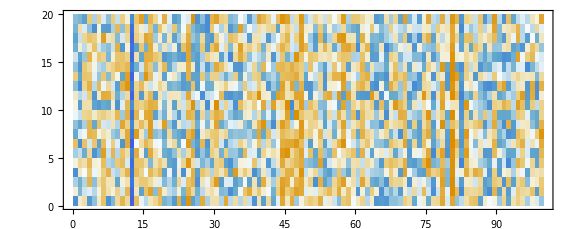

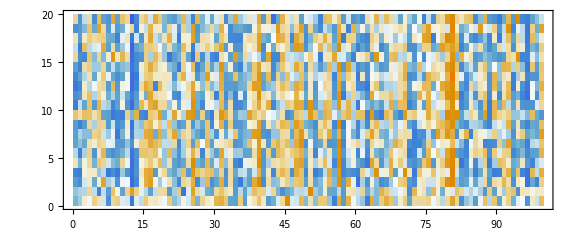

```mathematica
colanimals = Thread[{Range[Length[animals]], animals}];
colfruits = Thread[{Range[Length[fruits]], fruits}];
MatrixPlot[animalsVector, FrameTicks ->{None,None,colanimals,None},ImageSize -> Large]
MatrixPlot[fruitsVector, FrameTicks ->{None,None,colfruits,None},ImageSize -> Large]
```

These similarities can be better visualized using a FeatureSpacePlot:

```mathematica
FeatureSpacePlot[Join[animals, fruits], FeatureExtractor -> netWordEmbedding]
```

-Graphics-

### Contextual Words Embedding

The ELMo Contextual Word Representations model represent words as contextual word-embedding vectors.

```mathematica
netContextEmbedding = NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"];
```

For each token, the net produces three length-1024 feature vectors: one that is context-independent (port "Embedding") and two that are contextual (ports "ContextualEmbedding/1" and "ContextualEmbedding/2").

```mathematica
embeddings =netContextEmbedding["circular economy"];
embeddings2 = netContextEmbedding["neoclassical economy"];
```

The context-independent embedding for the same word is the same, whatever the surrounding text is. For instance, for the word "economy":

```mathematica
embeddings[["Embedding", 2]] == embeddings2[["Embedding", 2]]
```

True

The context-dependent embeddings are different for the same word in two different sentences:

```mathematica
embeddings[["ContextualEmbedding/1", 2]] == embeddings2[["ContextualEmbedding/1", 2]]
```

False

Suggested usage is to take the average of the context-independent & contextual embeddings.

```mathematica
netevaluateWithContext[sentence_String]:=With[
{tokenizedSentence=TextElement[StringSplit[sentence]]},
AssociationThread[
Thread[{First[tokenizedSentence],sentence}],Mean@Values@NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]@tokenizedSentence
]
]
```

```mathematica
embeddings=netevaluateWithContext["circular economy"];
Map[Dimensions,embeddings]
```

<|{circular,circular economy}→{1024},{economy,circular economy}→{1024}|>

### Text Embedding

The BERT model allows to represent text as sequence of vectors.
It is using "bidirectional self-attention", often referred to as a transformer encoder, meaning that the embedding of a given subword depends on the full input text.

The model produces feature vectors of size 768, which correspond to sequence of words, subwords, start and end of string.

```mathematica
text = "Today, the price of the most widely used fertilizer is surging, threatening crop yield worldwide. The reason is the increase in gas prices because fertiliser requires large amounts of gas in its production.";
```

```mathematica
netTextEmbedding = NetModel["BERT Trained on BookCorpus and Wikipedia Data"];
textEmbedding = netTextEmbedding[text];
```

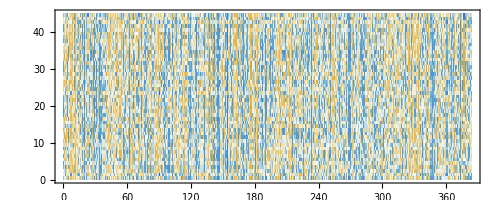

```mathematica
MatrixPlot@textEmbedding
```

## Useful links

Neural Nets documentation & functions

Introduction to Neural Nets in Wolfram